```mathematica
4186/349.228
```

11.9864

```mathematica
349.228/27.5
```

12.6992

```mathematica
√(27.5 4186)
```

339.286

```mathematica
Array[2^#1 3^#2&,{10,10},{-5,-5}]
```

{{1/7776,1/2592,1/864,1/288,1/96,1/32,3/32,9/32,27/32,81/32},{1/3888,1/1296,1/432,1/144,1/48,1/16,3/16,9/16,27/16,81/16},{1/1944,1/648,1/216,1/72,1/24,1/8,3/8,9/8,27/8,81/8},{1/972,1/324,1/108,1/36,1/12,1/4,3/4,9/4,27/4,81/4},{1/486,1/162,1/54,1/18,1/6,1/2,3/2,9/2,27/2,81/2},{1/243,1/81,1/27,1/9,1/3,1,3,9,27,81},{2/243,2/81,2/27,2/9,2/3,2,6,18,54,162},{4/243,4/81,4/27,4/9,4/3,4,12,36,108,324},{8/243,8/81,8/27,8/9,8/3,8,24,72,216,648},{16/243,16/81,16/27,16/9,16/3,16,48,144,432,1296}}

```mathematica
Reduce[-Log[2,13]<i-j +j Log[2,3]<Log[2,12],{i,j},Integers]
```

(i|j)∈Integers&&(i Log[2]+Log[13])/(Log[2]-Log[3])<j<(-2 Log[2]+i Log[2]-Log[3])/(Log[2]-Log[3])

```mathematica
{Floor[2.3],Ceiling[2.3]}
```

{2,3}

```mathematica
{Floor[-2.3],Ceiling[-2.3]}
```

{-3,-2}

```mathematica
Table[2^(i-j)3^j,{i,-2,2},{j,Ceiling[(i Log[2]+Log[13])/(Log[2]-Log[3])],Floor[(-2 Log[2]+i Log[2]-Log[3])/(Log[2]-Log[3])]}]
```

{{1/9,1/6,1/4,3/8,9/16,27/32,81/64,243/128,729/256,2187/512,6561/1024,19683/2048},{8/81,4/27,2/9,1/3,1/2,3/4,9/8,27/16,81/32,243/64,729/128,2187/256},{64/729,32/243,16/81,8/27,4/9,2/3,1,3/2,9/4,27/8,81/16,243/32,729/64},{512/6561,256/2187,128/729,64/243,32/81,16/27,8/9,4/3,2,3,9/2,27/4,81/8},{2048/19683,1024/6561,512/2187,256/729,128/243,64/81,32/27,16/9,8/3,4,6,9}}

```mathematica
Flatten[Table[2^(i-j)3^j,{i,-3,3},{j,Ceiling[(i Log[2]+Log[13])/(Log[2]-Log[3])],Floor[(-2 Log[2]+i Log[2]-Log[3])/(Log[2]-Log[3])]}]]
```

{1/12,1/8,3/16,9/32,27/64,81/128,243/256,729/512,2187/1024,6561/2048,19683/4096,59049/8192,177147/16384,1/9,1/6,1/4,3/8,9/16,27/32,81/64,243/128,729/256,2187/512,6561/1024,19683/2048,8/81,4/27,2/9,1/3,1/2,3/4,9/8,27/16,81/32,243/64,729/128,2187/256,64/729,32/243,16/81,8/27,4/9,2/3,1,3/2,9/4,27/8,81/16,243/32,729/64,512/6561,256/2187,128/729,64/243,32/81,16/27,8/9,4/3,2,3,9/2,27/4,81/8,2048/19683,1024/6561,512/2187,256/729,128/243,64/81,32/27,16/9,8/3,4,6,9,16384/177147,8192/59049,4096/19683,2048/6561,1024/2187,512/729,256/243,128/81,64/27,32/9,16/3,8,12}

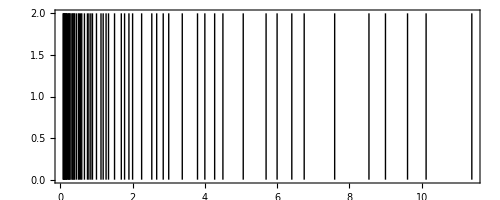

```mathematica
Graphics[Line[{{#,0},{#,2}}&/@Flatten[Table[2^(i-j)3^j,{i,-2,2},{j,Ceiling[(i Log[2]+Log[13])/(Log[2]-Log[3])],Floor[(-2 Log[2]+i Log[2]-Log[3])/(Log[2]-Log[3])]}]]],Frame->True]
```

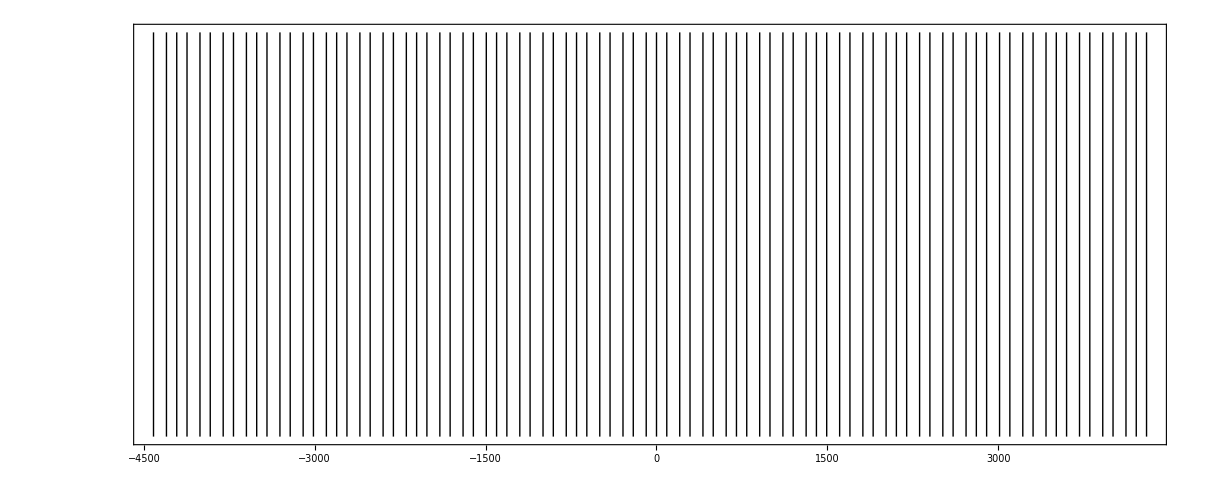

```mathematica
Graphics[Line[{{#,0},{#,200}}&/@(1200 Log[2,Flatten[Table[2^(i-j)3^j,{i,-3,3},{j,Ceiling[(i Log[2]+Log[13])/(Log[2]-Log[3])],Floor[(-2 Log[2]+i Log[2]-Log[3])/(Log[2]-Log[3])]}]]])],Frame->True,FrameTicks->{{None,None},{Automatic,None}}]
```

```mathematica
Differences[1200 Log[2,Sort[Flatten[Table[2^(i-j)3^j,{i,-4,4},{j,Ceiling[(i Log[2]+Log[13])/(Log[2]-Log[3])],Floor[(-2 Log[2]+i Log[2]-Log[3])/(Log[2]-Log[3])]}]]]]]//N
```

{90.225,23.46,90.225,90.225,23.46,90.225,90.225,113.685,90.225,90.225,23.46,90.225,90.225,23.46,90.225,90.225,113.685,90.225,90.225,23.46,90.225,90.225,23.46,90.225,90.225,113.685,90.225,90.225,23.46,90.225,90.225,23.46,90.225,90.225,113.685,90.225,90.225,23.46,90.225,90.225,23.46,90.225,90.225,113.685,90.225,90.225,23.46,90.225,90.225,23.46,90.225,90.225,113.685,90.225,90.225,23.46,90.225,90.225,23.46,90.225,90.225,113.685,90.225,90.225,23.46,90.225,90.225,23.46,90.225,90.225,113.685,90.225,90.225,23.46,90.225,90.225,23.46,90.225,90.225,113.685,90.225,90.225,23.46,90.225,90.225,23.46,90.225,90.225,113.685,90.225,90.225,23.46,90.225,90.225,23.46,90.225,90.225,113.685,90.225,90.225,23.46,90.225,90.225,23.46,90.225,90.225,113.685,90.225,90.225,23.46,90.225,90.225}

```mathematica
Table[1200.(m+n Log[2,3]),{m,-4,4},{n,-4,4}]
```

{{-12407.8,-10505.9,-8603.91,-6701.96,-4800.,-2898.04,-996.09,905.865,2807.82},{-11207.8,-9305.87,-7403.91,-5501.96,-3600.,-1698.04,203.91,2105.87,4007.82},{-10007.8,-8105.87,-6203.91,-4301.96,-2400.,-498.045,1403.91,3305.87,5207.82},{-8807.82,-6905.87,-5003.91,-3101.96,-1200.,701.955,2603.91,4505.87,6407.82},{-7607.82,-5705.87,-3803.91,-1901.96,0.,1901.96,3803.91,5705.87,7607.82},{-6407.82,-4505.87,-2603.91,-701.955,1200.,3101.96,5003.91,6905.87,8807.82},{-5207.82,-3305.87,-1403.91,498.045,2400.,4301.96,6203.91,8105.87,10007.8},{-4007.82,-2105.87,-203.91,1698.04,3600.,5501.96,7403.91,9305.87,11207.8},{-2807.82,-905.865,996.09,2898.04,4800.,6701.96,8603.91,10505.9,12407.8}}

```mathematica
iterquinte[list_]:=Union[Sort[Flatten[Union[NestWhileList[2#&,#1,2#<350&],NestWhileList[3/2#&,#1,2#<350&]]&/@list]]]
```

```mathematica
Last[FixedPointList[iterquinte[#]&,{1}]]
```

{1,3/2,2,9/4,3,27/8,4,9/2,81/16,6,27/4,243/32,8,9,81/8,729/64,12,27/2,243/16,16,2187/128,18,81/4,729/32,24,6561/256,27,243/8,32,2187/64,36,19683/512,81/2,729/16,48,6561/128,54,59049/1024,243/4,64,2187/32,72,19683/256,81,177147/2048,729/8,96,6561/64,108,59049/512,243/2,128,531441/4096,2187/16,144,19683/128,162,177147/1024,729/4,192,1594323/8192,6561/32,216,59049/256,243,256,531441/2048,2187/8,288,19683/64,324,177147/512}

```mathematica
Length[%]
```

72

```mathematica
N[Last[FixedPointList[iterquinte[#]&,{1}]]]
```

{1.,1.5,2.,2.25,3.,3.375,4.,4.5,5.0625,6.,6.75,7.59375,8.,9.,10.125,11.3906,12.,13.5,15.1875,16.,17.0859,18.,20.25,22.7813,24.,25.6289,27.,30.375,32.,34.1719,36.,38.4434,40.5,45.5625,48.,51.2578,54.,57.665,60.75,64.,68.3438,72.,76.8867,81.,86.4976,91.125,96.,102.516,108.,115.33,121.5,128.,129.746,136.688,144.,153.773,162.,172.995,182.25,192.,194.62,205.031,216.,230.66,243.,256.,259.493,273.375,288.,307.547,324.,345.99}

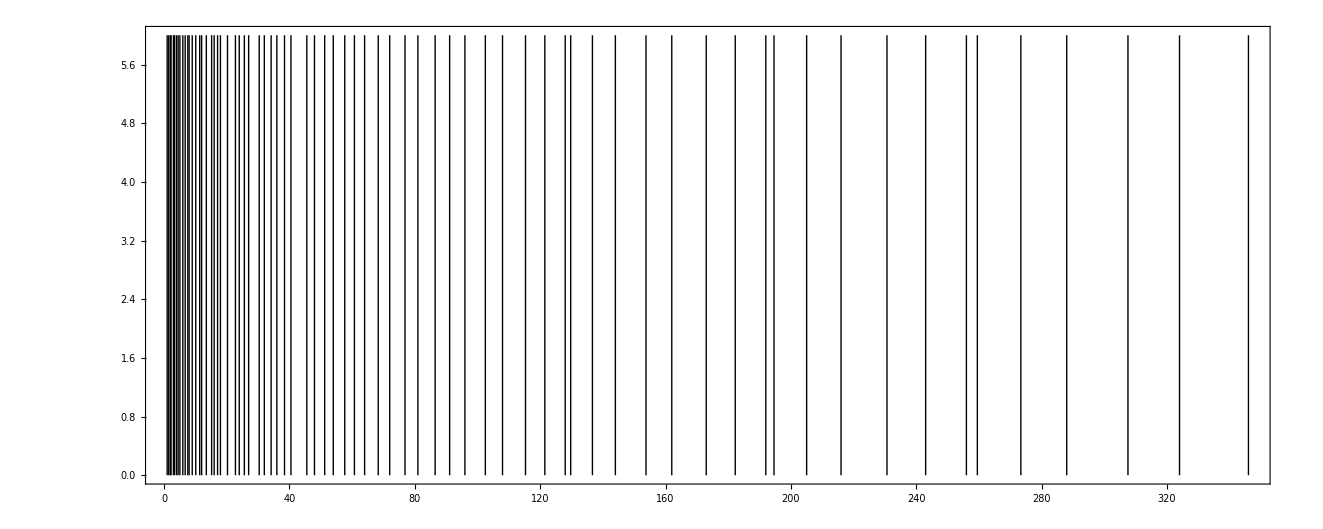

```mathematica
Graphics[Line[{{#,0},{#,6}}&/@Last[FixedPointList[iterquinte[#]&,{1}]]],Frame->True]
```

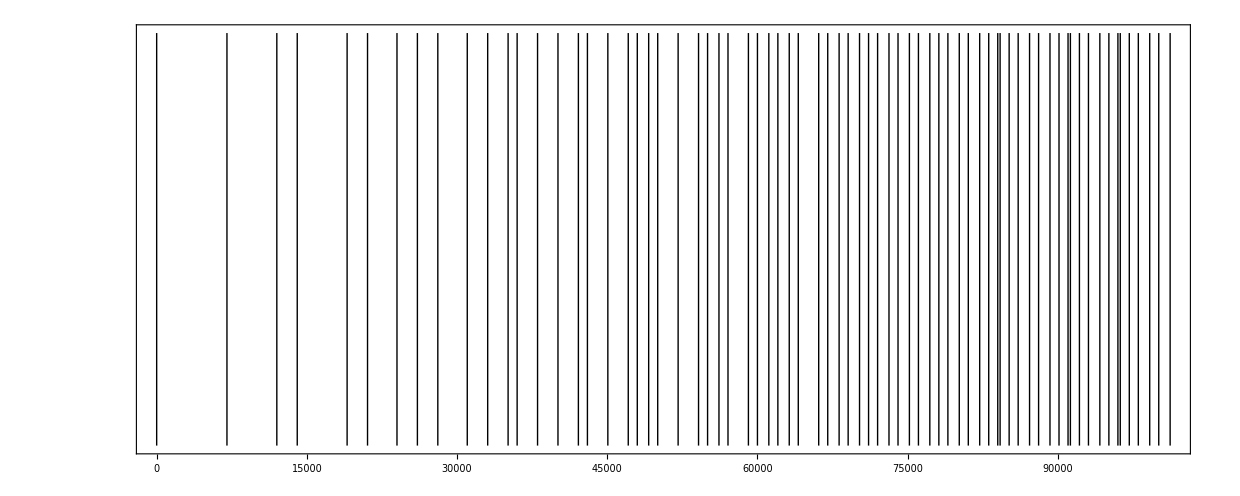

```mathematica
Graphics[Line[{{10#,0},{10#,2000}}&/@(1200 Log[2,Last[FixedPointList[iterquinte[#]&,{1}]]])],Frame->True,FrameTicks->{{None,None},{Automatic,None}}]
```

```mathematica
(1200. Log[2,Last[FixedPointList[iterquinte[#]&,{1}]]])                (*Intervalles en cents entre les notes : seuil environ 5 cents sauf aux basses fréquences *)
```

{0.,701.955,1200.,1403.91,1901.96,2105.87,2400.,2603.91,2807.82,3101.96,3305.87,3509.78,3600.,3803.91,4007.82,4211.73,4301.96,4505.87,4709.78,4800.,4913.69,5003.91,5207.82,5411.73,5501.96,5615.64,5705.87,5909.78,6000.,6113.69,6203.91,6317.6,6407.82,6611.73,6701.96,6815.64,6905.87,7019.55,7109.78,7200.,7313.69,7403.91,7517.6,7607.82,7721.51,7811.73,7901.96,8015.64,8105.87,8219.55,8309.78,8400.,8423.46,8513.69,8603.91,8717.6,8807.82,8921.51,9011.73,9101.96,9125.42,9215.64,9305.87,9419.55,9509.78,9600.,9623.46,9713.69,9803.91,9917.6,10007.8,10121.5}

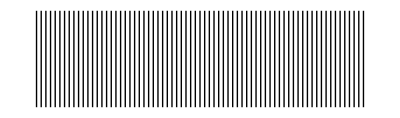

```mathematica
Graphics[Line[{{10#,0},{10#,12}}&/@Log[Table[2^(k/12) ,{k,0,70}]]]]
```

```mathematica
Graphics[Line[Table[{{0,Mod[(4/3)^n,2]},{12,Mod[(4/3)^n,2]}},{n,0,15}]]]
```

```mathematica
iter[list_]:=Union[Sort[Flatten[Union[NestWhileList[2#&,#1,2#<350&],NestWhileList[3/2#&,#1,2#<350&],NestWhileList[4/3#&,#1,2#<350&],NestWhileList[5/4#&,#1,2#<350&]]&/@list]]]
```

```mathematica
Last[FixedPointList[iter[#]&,{1}]]
```

{1,5/4,4/3,3/2,25/16,5/3,16/9,15/8,125/64,2,25/12,20/9,9/4,75/32,64/27,625/256,5/2,125/48,8/3,25/9,45/16,375/128,80/27,3,3125/1024,25/8,256/81,625/192,10/3,27/8,125/36,225/64,32/9,1875/512,100/27,15/4,15625/4096,125/32,320/81,4,3125/768,25/6,1024/243,135/32,625/144,1125/256,40/9,9/2,9375/2048,125/27,75/16,128/27,78125/16384,625/128,400/81,5,81/16,15625/3072,125/24,1280/243,675/128,16/3,3125/576,5625/1024,50/9,4096/729,45/8,46875/8192,625/108,375/64,160/27,390625/65536,6,3125/512,500/81,25/4,512/81,405/64,78125/12288,625/96,1600/243,3375/512,20/3,27/4,15625/2304,28125/4096,125/18,5120/729,225/32,64/9,234375/32768,3125/432,1875/256,200/27,1953125/262144,16384/2187,15/2,243/32,15625/2048,625/81,125/16,640/81,2025/256,390625/49152,8,3125/384,2000/243,16875/2048,25/3,2048/243,135/16,78125/9216,140625/16384,625/72,6400/729,1125/128,80/9,1171875/131072,9,15625/1728,9375/1024,250/27,9765625/1048576,20480/2187,75/8,256/27,1215/128,78125/8192,3125/324,625/64,800/81,10125/1024,1953125/196608,65536/6561,10,81/8,15625/1536,2500/243,84375/8192,125/12,2560/243,675/64,390625/36864,32/3,703125/65536,3125/288,8000/729,5625/512,100/9,5859375/524288,8192/729,45/4,78125/6912,729/64,46875/4096,625/54,48828125/4194304,25600/2187,375/32,320/27,6075/512,390625/32768,12,15625/1296,3125/256,1000/81,50625/4096,9765625/786432,81920/6561,25/2,1024/81,405/32,78125/6144,3125/243,421875/32768,625/48,3200/243,3375/256,1953125/147456,262144/19683,40/3,3515625/262144,27/2,15625/1152,10000/729,28125/2048,125/9,29296875/2097152,10240/729,225/16,390625/27648,128/9,3645/256,234375/16384,3125/216,244140625/16777216,32000/2187,1875/128,400/27,30375/2048,1953125/131072,32768/2187,15,78125/5184,243/16,15625/1024,1250/81,253125/16384,48828125/3145728,102400/6561,125/8,1280/81,2025/128,390625/24576,16,15625/972,2109375/131072,3125/192,4000/243,16875/1024,9765625/589824,327680/19683,50/3,17578125/1048576,4096/243,135/8,78125/4608,2187/128,12500/729,140625/8192,625/36,146484375/8388608,12800/729,1125/64,1953125/110592,1048576/59049,160/9,18225/1024,1171875/65536,18,15625/864,1220703125/67108864,40000/2187,9375/512,500/27,151875/8192,9765625/524288,40960/2187,75/4,390625/20736,512/27,1215/64,78125/4096,3125/162,1265625/65536,244140625/12582912,128000/6561,625/32,1600/81,10125/512,1953125/98304,131072/6561,20,78125/3888,10546875/524288,81/4,15625/768,5000/243,84375/4096,48828125/2359296,409600/19683,125/6,87890625/4194304,5120/243,675/32,390625/18432,64/3,10935/512,15625/729,703125/32768,3125/144,732421875/33554432,16000/729,5625/256,9765625/442368,1310720/59049,200/9,91125/4096,5859375/262144,16384/729,45/2,78125/3456,6103515625/268435456,729/32,50000/2187,46875/2048,625/27,759375/32768,48828125/2097152,51200/2187,375/16,1953125/82944,4194304/177147,640/27,6075/256,390625/16384,24,15625/648,6328125/262144,1220703125/50331648,160000/6561,3125/128,2000/81,50625/2048,9765625/393216,163840/6561,25,390625/15552,52734375/2097152,2048/81,405/16,78125/3072,6561/256,6250/243,421875/16384,244140625/9437184,512000/19683,625/24,439453125/16777216,6400/243,3375/128,1953125/73728,524288/19683,80/3,54675/2048,78125/2916,3515625/131072,27,15625/576,3662109375/134217728,20000/729,28125/1024,48828125/1769472,1638400/59049,250/9,455625/16384,29296875/1048576,20480/729,225/8,390625/13824,30517578125/1073741824,256/9,3645/128,62500/2187,234375/8192,3125/108,3796875/131072,244140625/8388608,64000/2187,1875/64,9765625/331776,5242880/177147,800/27,30375/1024,1953125/65536,65536/2187,30,78125/2592,31640625/1048576,6103515625/201326592,243/8,200000/6561,15625/512,2500/81,253125/8192,48828125/1572864,204800/6561,125/4,1953125/62208,263671875/8388608,16777216/531441,2560/81,2025/64,390625/12288,32,32805/1024,15625/486,2109375/65536,1220703125/37748736,640000/19683,3125/96,2197265625/67108864,8000/243,16875/512,9765625/294912,655360/19683,100/3,273375/8192,390625/11664,17578125/524288,8192/243,135/4,78125/2304,18310546875/536870912,2187/64,25000/729,140625/4096,244140625/7077888,2048000/59049,625/18,2278125/65536,146484375/4194304,25600/729,1125/32,1953125/55296,2097152/59049,152587890625/4294967296,320/9,18225/512,78125/2187,1171875/32768,36,15625/432,18984375/524288,1220703125/33554432,80000/2187,9375/256,48828125/1327104,6553600/177147,1000/27,151875/4096,9765625/262144,81920/2187,75/2,390625/10368,158203125/4194304,30517578125/805306368,1024/27,1215/32,250000/6561,78125/2048,19683/512,3125/81,1265625/32768,244140625/6291456,256000/6561,625/16,9765625/248832,1318359375/33554432,20971520/531441,3200/81,10125/256,1953125/49152,262144/6561,40,164025/4096,78125/1944,10546875/262144,6103515625/150994944,81/2,800000/19683,15625/384,10986328125/268435456,10000/243,84375/2048,48828125/1179648,819200/19683,125/3,1366875/32768,1953125/46656,87890625/2097152,67108864/1594323,10240/243,675/16,390625/9216,91552734375/2147483648,128/3,10935/256,31250/729,703125/16384,1220703125/28311552,2560000/59049,3125/72,11390625/262144,732421875/16777216,32000/729,5625/128,9765625/221184,2621440/59049,762939453125/17179869184,400/9,91125/2048,390625/8748,5859375/131072,32768/729,45,78125/1728,94921875/2097152,6103515625/134217728,729/16,100000/2187,46875/1024,244140625/5308416,8192000/177147,1250/27,759375/16384,48828125/1048576,102400/2187,375/8,1953125/41472,791015625/16777216,8388608/177147,152587890625/3221225472,1280/27,6075/128,312500/6561,390625/8192,48,98415/2048,15625/324,6328125/131072,1220703125/25165824,320000/6561,3125/64,48828125/995328,6591796875/134217728,26214400/531441,4000/81,50625/1024,9765625/196608,327680/6561,50,820125/16384,390625/7776,52734375/1048576,30517578125/603979776,4096/81,405/8,1000000/19683,78125/1536,54931640625/1073741824,6561/128,12500/243,421875/8192,244140625/4718592,1024000/19683,625/12,6834375/131072,9765625/186624,439453125/8388608,83886080/1594323,12800/243,3375/64,1953125/36864,1048576/19683,457763671875/8589934592,160/3,54675/1024,78125/1458,3515625/65536,6103515625/113246208,54,3200000/59049,15625/288,56953125/1048576,3662109375/67108864,40000/729,28125/512,48828125/884736,3276800/59049,3814697265625/68719476736,500/9,455625/8192,1953125/34992,29296875/524288,268435456/4782969,40960/729,225/4,390625/6912,474609375/8388608,30517578125/536870912,512/9,3645/64,125000/2187,234375/4096,1220703125/21233664,59049/1024,10240000/177147,3125/54,3796875/65536,244140625/4194304,128000/2187,1875/32,9765625/165888,3955078125/67108864,10485760/177147,762939453125/12884901888,1600/27,30375/512,390625/6561,1953125/32768,131072/2187,60,492075/8192,78125/1296,31640625/524288,6103515625/100663296,243/4,400000/6561,15625/256,244140625/3981312,32958984375/536870912,32768000/531441,5000/81,253125/4096,48828125/786432,409600/6561,125/2,4100625/65536,1953125/31104,263671875/4194304,33554432/531441,152587890625/2415919104,5120/81,2025/32,1250000/19683,390625/6144,274658203125/4294967296,64,32805/512,15625/243,2109375/32768,1220703125/18874368,1280000/19683,3125/48,34171875/524288,48828125/746496,2197265625/33554432,104857600/1594323,16000/243,16875/256,9765625/147456,1310720/19683,2288818359375/34359738368,200/3,273375/4096,390625/5832,17578125/262144,30517578125/452984832,16384/243,135/2,4000000/59049,78125/1152,284765625/4194304,18310546875/268435456,2187/32,50000/729,140625/2048,244140625/3538944,4096000/59049,19073486328125/274877906944,625/9,2278125/32768,9765625/139968,146484375/2097152,335544320/4782969,51200/729,1125/16,1953125/27648,2373046875/33554432,4194304/59049,152587890625/2147483648,640/9,18225/256,156250/2187,1171875/16384,6103515625/84934656,72,295245/4096,12800000/177147,15625/216,18984375/262144,1220703125/16777216,160000/2187,9375/128,48828125/663552,19775390625/268435456,13107200/177147,3814697265625/51539607552,2000/27,151875/2048,1953125/26244,9765625/131072,1073741824/14348907,163840/2187,75,2460375/32768,390625/5184,158203125/2097152,30517578125/402653184,2048/27,1215/16,500000/6561,78125/1024,1220703125/15925248,164794921875/2147483648,19683/256,40960000/531441,6250/81,1265625/16384,244140625/3145728,512000/6561,625/8,20503125/262144,9765625/124416,1318359375/16777216,41943040/531441,762939453125/9663676416,6400/81,10125/128,1562500/19683,1953125/24576,524288/6561,1373291015625/17179869184,80,164025/2048,78125/972,10546875/131072,6103515625/75497472,81,1600000/19683,15625/192,170859375/2097152,244140625/2985984,10986328125/134217728,131072000/1594323,20000/243,84375/1024,48828125/589824,1638400/19683,11444091796875/137438953472,250/3,1366875/16384,1953125/23328,87890625/1048576,134217728/1594323,152587890625/1811939328,20480/243,675/8,5000000/59049,390625/4608,1423828125/16777216,91552734375/1073741824,256/3,10935/128,62500/729,703125/8192,1220703125/14155776,177147/2048,5120000/59049,95367431640625/1099511627776,3125/36,11390625/131072,48828125/559872,732421875/8388608,419430400/4782969,64000/729,5625/64,9765625/110592,11865234375/134217728,5242880/59049,762939453125/8589934592,800/9,91125/1024,390625/4374,5859375/65536,30517578125/339738624,65536/729,90,1476225/16384,16000000/177147,78125/864,94921875/1048576,6103515625/67108864,729/8,200000/2187,46875/512,244140625/2654208,98876953125/1073741824,16384000/177147,19073486328125/206158430208,2500/27,759375/8192,9765625/104976,48828125/524288,1342177280/14348907,204800/2187,375/4,12301875/131072,1953125/20736,791015625/8388608,16777216/177147,152587890625/1610612736,2560/27,6075/64,625000/6561,390625/4096,6103515625/63700992,823974609375/8589934592,96,98415/1024,51200000/531441,15625/162,6328125/65536,1220703125/12582912,640000/6561,3125/32,102515625/1048576,48828125/497664,6591796875/67108864,52428800/531441,3814697265625/38654705664,8000/81,50625/512,1953125/19683,9765625/98304,4294967296/43046721,655360/6561,6866455078125/68719476736,100,820125/8192,390625/3888,52734375/524288,30517578125/301989888,8192/81,405/4,2000000/19683,78125/768,854296875/8388608,1220703125/11943936,54931640625/536870912,6561/64,163840000/1594323,25000/243,421875/4096,244140625/2359296,2048000/19683,57220458984375/549755813888,625/6,6834375/65536,9765625/93312,439453125/4194304,167772160/1594323,762939453125/7247757312,25600/243,3375/32,6250000/59049,1953125/18432,7119140625/67108864,2097152/19683,457763671875/4294967296,320/3,54675/512,78125/729,3515625/32768,6103515625/56623104,108,885735/8192,6400000/59049,476837158203125/4398046511104,15625/144,56953125/524288,244140625/2239488,3662109375/33554432,524288000/4782969,80000/729,28125/256,48828125/442368,59326171875/536870912,6553600/59049,3814697265625/34359738368,1000/9,455625/4096,1953125/17496,29296875/262144,536870912/4782969,152587890625/1358954496,81920/729,225/2,7381125/65536,20000000/177147,390625/3456,474609375/4194304,30517578125/268435456,1024/9,3645/32,250000/2187,234375/2048,1220703125/10616832,494384765625/4294967296,59049/512,20480000/177147,95367431640625/824633720832,3125/27,3796875/32768,48828125/419904,244140625/2097152,1677721600/14348907,256000/2187,1875/16,61509375/524288,9765625/82944,3955078125/33554432,20971520/177147,762939453125/6442450944,3200/27,30375/256,781250/6561,1953125/16384,30517578125/254803968,262144/2187,4119873046875/34359738368,120,492075/4096,64000000/531441,78125/648,31640625/262144,6103515625/50331648,243/2,800000/6561,15625/128,512578125/4194304,244140625/1990656,32958984375/268435456,65536000/531441,19073486328125/154618822656,10000/81,253125/2048,9765625/78732,48828125/393216,5368709120/43046721,819200/6561,34332275390625/274877906944,125,4100625/32768,1953125/15552,263671875/2097152,67108864/531441,152587890625/1207959552,10240/81,2025/16,2500000/19683,390625/3072,4271484375/33554432,6103515625/47775744,274658203125/2147483648,128,32805/256,204800000/1594323,31250/243,2109375/16384,1220703125/9437184,531441/4096,2560000/19683,286102294921875/2199023255552,3125/24,34171875/262144,48828125/373248,2197265625/16777216,209715200/1594323,3814697265625/28991029248,32000/243,16875/128,7812500/59049,9765625/73728,35595703125/268435456,17179869184/129140163,2621440/19683,2288818359375/17179869184,400/3,273375/2048,390625/2916,17578125/131072,30517578125/226492416,32768/243,135,4428675/32768,8000000/59049,2384185791015625/17592186044416,78125/576,284765625/2097152,1220703125/8957952,18310546875/134217728,2187/16,655360000/4782969,100000/729,140625/1024,244140625/1769472,296630859375/2147483648,8192000/59049,19073486328125/137438953472,1250/9,2278125/16384,9765625/69984,146484375/1048576,671088640/4782969,762939453125/5435817984,102400/729,1125/8,36905625/262144,25000000/177147,1953125/13824,2373046875/16777216,8388608/59049,152587890625/1073741824,1280/9,18225/128,312500/2187,1171875/8192,6103515625/42467328,2471923828125/17179869184,144,295245/2048,25600000/177147,476837158203125/3298534883328,15625/108,18984375/131072,244140625/1679616,1220703125/8388608,2097152000/14348907,320000/2187,9375/64,307546875/2097152,48828125/331776,19775390625/134217728,26214400/177147,3814697265625/25769803776,4000/27,151875/1024,1953125/13122,9765625/65536,2147483648/14348907,152587890625/1019215872,327680/2187,20599365234375/137438953472,150,2460375/16384,80000000/531441,390625/2592,158203125/1048576,30517578125/201326592,4096/27,1215/8,1000000/6561,78125/512,2562890625/16777216,1220703125/7962624,164794921875/1073741824,19683/128,81920000/531441,95367431640625/618475290624,12500/81,1265625/8192,48828125/314928,244140625/1572864,6710886400/43046721,1024000/6561,171661376953125/1099511627776,625/4,20503125/131072,9765625/62208,1318359375/8388608,83886080/531441,762939453125/4831838208,12800/81,10125/64,3125000/19683,1953125/12288,21357421875/134217728,30517578125/191102976,1048576/6561,1373291015625/8589934592,160,164025/1024,256000000/1594323,78125/486,10546875/65536,6103515625/37748736,162,2657205/16384,3200000/19683,1430511474609375/8796093022208,15625/96,170859375/1048576,244140625/1492992,10986328125/67108864,262144000/1594323,19073486328125/115964116992,40000/243,84375/512,9765625/59049,48828125/294912,177978515625/1073741824,21474836480/129140163,3276800/19683,11444091796875/68719476736,500/3,1366875/8192,1953125/11664,87890625/524288,268435456/1594323,152587890625/905969664,40960/243,675/4,22143375/131072,10000000/59049,11920928955078125/70368744177664,390625/2304,1423828125/8388608,6103515625/35831808,91552734375/536870912,512/3,10935/64,819200000/4782969,125000/729,703125/4096,1220703125/7077888,1483154296875/8589934592,177147/1024,10240000/59049,95367431640625/549755813888,3125/18,11390625/65536,48828125/279936,732421875/4194304,838860800/4782969,3814697265625/21743271936,128000/729,5625/32,184528125/1048576,31250000/177147,9765625/55296,11865234375/67108864,68719476736/387420489,10485760/59049,762939453125/4294967296,1600/9,91125/512,390625/2187,5859375/32768,30517578125/169869312,131072/729,12359619140625/68719476736,180,1476225/8192,32000000/177147,2384185791015625/13194139533312,78125/432,94921875/524288,1220703125/6718464,6103515625/33554432,729/4,2621440000/14348907,400000/2187,46875/256,1537734375/8388608,244140625/1327104,98876953125/536870912,32768000/177147,19073486328125/103079215104,5000/27,759375/4096,9765625/52488,48828125/262144,2684354560/14348907,762939453125/4076863488,409600/2187,102996826171875/549755813888,375/2,12301875/65536,100000000/531441,1953125/10368,791015625/4194304,33554432/177147,152587890625/805306368,5120/27,6075/32,1250000/6561,390625/2048,12814453125/67108864,6103515625/31850496,823974609375/4294967296,192,98415/512,102400000/531441,476837158203125/2473901162496,15625/81,6328125/32768,244140625/1259712,1220703125/6291456,1594323/8192,8388608000/43046721,1280000/6561,858306884765625/4398046511104,3125/16,102515625/524288,48828125/248832,6591796875/33554432,104857600/531441,3814697265625/19327352832,16000/81,50625/256,3906250/19683,9765625/49152,106787109375/536870912,8589934592/43046721,152587890625/764411904,1310720/6561,6866455078125/34359738368,200,820125/4096,320000000/1594323,390625/1944,52734375/262144,30517578125/150994944,16384/81,405/2,13286025/65536,4000000/19683,7152557373046875/35184372088832,78125/384,854296875/4194304,1220703125/5971968,54931640625/268435456,6561/32,327680000/1594323,95367431640625/463856467968,50000/243,421875/2048,48828125/236196,244140625/1179648,889892578125/4294967296,26843545600/129140163,4096000/19683,57220458984375/274877906944,625/3,6834375/32768,9765625/46656,439453125/2097152,335544320/1594323,762939453125/3623878656,51200/243,3375/16,110716875/524288,12500000/59049,59604644775390625/281474976710656,1953125/9216,7119140625/33554432,30517578125/143327232,4194304/19683,457763671875/2147483648,640/3,54675/256,1024000000/4782969,156250/729,3515625/16384,6103515625/28311552,7415771484375/34359738368,216,885735/4096,12800000/59049,476837158203125/2199023255552,15625/72,56953125/262144,244140625/1119744,3662109375/16777216,1048576000/4782969,19073486328125/86973087744,160000/729,28125/128,922640625/4194304,39062500/177147,48828125/221184,59326171875/268435456,85899345920/387420489,13107200/59049,3814697265625/17179869184,2000/9,455625/2048,1953125/8748,29296875/131072,1073741824/4782969,152587890625/679477248,163840/729,61798095703125/274877906944,225,7381125/32768,40000000/177147,11920928955078125/52776558133248,390625/1728,474609375/2097152,6103515625/26873856,30517578125/134217728,2048/9,3645/16,3276800000/14348907,500000/2187,234375/1024,7688671875/33554432,1220703125/5308416,494384765625/2147483648,59049/256,40960000/177147,95367431640625/412316860416,6250/27,3796875/16384,48828125/209952,244140625/1048576,3355443200/14348907,512000/2187,514984130859375/2199023255552,1875/8,61509375/262144,9765625/41472,3955078125/16777216,41943040/177147,762939453125/3221225472,6400/27,30375/128,1562500/6561,1953125/8192,64072265625/268435456,30517578125/127401984,524288/2187,4119873046875/17179869184,240,492075/2048,128000000/531441,78125/324,31640625/131072,6103515625/25165824,243,7971615/32768,1600000/6561,4291534423828125/17592186044416,15625/64,512578125/2097152,244140625/995328,32958984375/134217728,131072000/531441,19073486328125/77309411328,20000/81,253125/1024,9765625/39366,48828125/196608,533935546875/2147483648,10737418240/43046721,1638400/6561,34332275390625/137438953472,250,4100625/16384,1953125/7776,263671875/1048576,134217728/531441,152587890625/603979776,20480/81,2025/8,66430125/262144,5000000/19683,35762786865234375/140737488355328,390625/1536,4271484375/16777216,6103515625/23887872,274658203125/1073741824,256,32805/128,409600000/1594323,62500/243,2109375/8192,1220703125/4718592,4449462890625/17179869184,531441/2048,5120000/19683,286102294921875/1099511627776,3125/12,34171875/131072,48828125/186624,2197265625/8388608,419430400/1594323,3814697265625/14495514624,64000/243,16875/64,15625000/59049,9765625/36864,35595703125/134217728,34359738368/129140163,5242880/19683,2288818359375/8589934592,800/3,273375/1024,390625/1458,17578125/65536,30517578125/113246208,65536/243,270,4428675/16384,16000000/59049,2384185791015625/8796093022208,78125/288,284765625/1048576,1220703125/4478976,18310546875/67108864,2187/8,1310720000/4782969,200000/729,140625/512,244140625/884736,296630859375/1073741824,16384000/59049,19073486328125/68719476736,2500/9,2278125/8192,9765625/34992,146484375/524288,1342177280/4782969,762939453125/2717908992,204800/729,1125/4,36905625/131072,50000000/177147,1953125/6912,2373046875/8388608,16777216/59049,152587890625/536870912,2560/9,18225/64,625000/2187,1171875/4096,6103515625/21233664,2471923828125/8589934592,288,295245/1024,51200000/177147,476837158203125/1649267441664,15625/54,18984375/65536,244140625/839808,1220703125/4194304,4194304000/14348907,640000/2187,9375/32,307546875/1048576,48828125/165888,19775390625/67108864,52428800/177147,3814697265625/12884901888,8000/27,151875/512,1953125/6561,9765625/32768,4294967296/14348907,152587890625/509607936,655360/2187,20599365234375/68719476736,300,2460375/8192,160000000/531441,390625/1296,158203125/524288,30517578125/100663296,8192/27,1215/4,2000000/6561,78125/256,2562890625/8388608,1220703125/3981312,164794921875/536870912,19683/64,163840000/531441,95367431640625/309237645312,25000/81,1265625/4096,48828125/157464,244140625/786432,13421772800/43046721,2048000/6561,171661376953125/549755813888,625/2,20503125/65536,9765625/31104,1318359375/4194304,167772160/531441,762939453125/2415919104,25600/81,10125/32,6250000/19683,1953125/6144,21357421875/67108864,30517578125/95551488,2097152/6561,1373291015625/4294967296,320,164025/512,512000000/1594323,78125/243,10546875/32768,6103515625/18874368,324,2657205/8192,6400000/19683,1430511474609375/4398046511104,15625/48,170859375/524288,244140625/746496,10986328125/33554432,524288000/1594323,19073486328125/57982058496,80000/243,84375/256,19531250/59049,48828125/147456,177978515625/536870912,42949672960/129140163,6553600/19683,11444091796875/34359738368,1000/3,1366875/4096,1953125/5832,87890625/262144,536870912/1594323,152587890625/452984832,81920/243,675/2,22143375/65536,20000000/59049,11920928955078125/35184372088832,390625/1152,1423828125/4194304,6103515625/17915904,91552734375/268435456,1024/3,10935/32,1638400000/4782969,250000/729,703125/2048,1220703125/3538944,1483154296875/4294967296,177147/512,20480000/59049,95367431640625/274877906944,3125/9,11390625/32768,48828125/139968,732421875/2097152}

```mathematica
Length[%]
```

1554

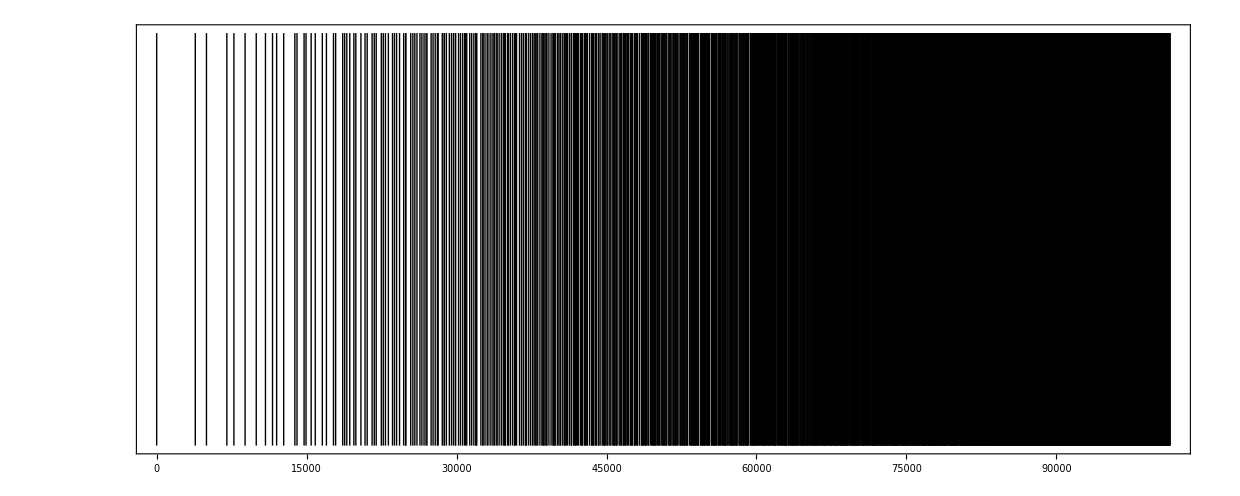

```mathematica
Graphics[Line[{{10#,0},{10#,2000}}&/@(1200 Log[2,Last[FixedPointList[iter[#]&,{1}]]])],Frame->True,FrameTicks->{{None,None},{Automatic,None}}]
```

```mathematica
(1200. Log[2,Last[FixedPointList[iter[#]&,{1}]]])                (*Intervalles en cents entre les notes : seuil d'environ 4 cents vers 1500 Hz, remonte vers 8 cents aux plus hautes fréquences et remonte plus sérieusement vers 40 cents aux basses fréquences *)
```

{0.,386.314,498.045,701.955,772.627,884.359,996.09,1088.27,1158.94,1200.,1270.67,1382.4,1403.91,1474.58,1494.13,1545.25,1586.31,1656.99,1698.04,1768.72,1790.22,1860.9,1880.45,1901.96,1931.57,1972.63,1992.18,2043.3,2084.36,2105.87,2155.03,2176.54,2196.09,2247.21,2266.76,2288.27,2317.88,2358.94,2378.49,2400.,2429.61,2470.67,2490.22,2492.18,2541.34,2562.85,2582.4,2603.91,2633.52,2653.08,2674.58,2694.13,2704.2,2745.25,2764.81,2786.31,2807.82,2815.93,2856.99,2876.54,2878.49,2898.04,2927.66,2949.16,2968.72,2988.27,2990.22,3019.84,3039.39,3060.9,3080.45,3090.51,3101.96,3131.57,3151.12,3172.63,3192.18,3194.13,3202.24,3243.3,3262.85,3264.81,3284.36,3305.87,3313.97,3335.48,3355.03,3374.58,3376.54,3396.09,3406.15,3425.7,3447.21,3466.76,3476.82,3486.31,3488.27,3509.78,3517.88,3537.43,3558.94,3578.49,3580.45,3588.55,3600.,3629.61,3649.17,3651.12,3670.67,3690.22,3692.18,3700.29,3721.79,3741.34,3760.9,3762.85,3782.4,3792.46,3803.91,3812.02,3833.52,3853.08,3863.14,3872.63,3874.58,3894.13,3896.09,3904.2,3923.75,3945.25,3964.81,3966.76,3974.87,3984.36,3986.31,4007.82,4015.93,4035.48,4037.43,4056.99,4076.54,4078.49,4086.6,4098.04,4108.11,4127.66,4147.21,4149.16,4168.72,4178.78,4188.27,4190.22,4198.33,4211.73,4219.84,4239.39,4249.45,4258.94,4260.9,4280.45,4282.4,4290.51,4301.96,4310.06,4331.57,4351.12,4353.07,4361.18,4370.67,4372.63,4392.18,4394.13,4402.24,4421.79,4423.75,4443.3,4462.85,4464.81,4472.91,4482.4,4484.36,4494.42,4505.87,4513.97,4533.52,4535.48,4555.03,4565.09,4574.58,4576.54,4584.64,4596.09,4598.04,4606.15,4625.7,4635.76,4645.26,4647.21,4666.76,4668.72,4676.82,4686.31,4688.27,4696.38,4709.78,4717.88,4737.43,4739.39,4747.5,4756.99,4758.94,4778.49,4780.45,4788.55,4800.,4808.11,4810.06,4829.61,4849.17,4851.12,4859.23,4868.72,4870.67,4880.73,4890.22,4892.18,4900.29,4913.69,4919.84,4921.79,4941.34,4951.41,4960.9,4962.85,4970.96,4980.45,4982.4,4984.36,4992.46,5003.91,5012.02,5022.08,5031.57,5033.52,5053.08,5055.03,5063.14,5072.63,5074.58,5082.69,5094.13,5096.09,5104.2,5123.75,5125.7,5133.81,5143.3,5145.25,5164.81,5166.76,5174.87,5184.36,5186.31,5194.42,5196.37,5207.82,5215.93,5235.48,5237.43,5245.54,5255.03,5256.99,5267.05,5276.54,5278.49,5286.6,5298.04,5300.,5306.15,5308.11,5327.66,5337.72,5347.21,5349.16,5357.27,5366.76,5368.72,5370.67,5378.78,5388.27,5390.22,5398.33,5408.39,5411.73,5417.88,5419.84,5439.39,5441.34,5449.45,5458.94,5460.9,5469.,5478.49,5480.45,5482.4,5490.51,5501.96,5510.06,5512.02,5520.12,5529.61,5531.57,5551.12,5553.07,5561.18,5570.67,5572.63,5580.73,5582.69,5592.18,5594.13,5602.24,5615.64,5621.79,5623.75,5631.85,5641.35,5643.3,5653.36,5662.85,5664.81,5672.91,5682.4,5684.36,5686.31,5692.47,5694.42,5705.87,5713.97,5724.03,5733.52,5735.48,5743.59,5753.08,5755.03,5756.98,5765.09,5774.58,5776.54,5784.64,5794.71,5796.09,5798.04,5804.2,5806.15,5825.7,5827.66,5835.76,5845.26,5847.21,5855.32,5864.81,5866.76,5868.72,5876.82,5886.31,5888.27,5896.38,5898.33,5906.44,5909.78,5915.93,5917.88,5937.43,5939.39,5947.5,5956.99,5958.94,5967.05,5969.,5976.54,5978.49,5980.45,5988.55,6000.,6001.95,6008.11,6010.06,6018.17,6027.66,6029.61,6039.67,6049.17,6051.12,6059.23,6068.72,6070.67,6072.63,6078.78,6080.73,6090.22,6092.18,6100.29,6110.35,6113.69,6119.84,6121.79,6129.9,6139.39,6141.34,6143.3,6151.41,6160.9,6162.85,6170.96,6180.45,6181.02,6182.4,6184.36,6190.51,6192.46,6203.91,6212.02,6213.97,6222.08,6231.57,6233.52,6241.63,6251.12,6253.08,6255.03,6263.14,6272.63,6274.58,6282.69,6284.64,6292.75,6294.13,6296.09,6302.24,6304.2,6317.6,6323.75,6325.7,6333.81,6343.3,6345.25,6353.36,6355.32,6362.85,6364.81,6366.76,6374.87,6384.36,6386.31,6388.27,6394.42,6396.37,6404.48,6407.82,6413.97,6415.93,6425.99,6435.48,6437.43,6445.54,6455.03,6456.99,6458.94,6465.09,6467.05,6474.58,6476.54,6478.49,6486.6,6496.66,6498.04,6500.,6506.15,6508.11,6516.21,6525.7,6527.66,6529.61,6537.72,6547.21,6549.16,6557.27,6566.76,6567.33,6568.72,6570.67,6576.82,6578.78,6588.27,6590.22,6598.33,6600.28,6608.39,6611.73,6617.88,6619.84,6627.94,6637.44,6639.39,6641.34,6649.45,6658.94,6660.9,6669.,6670.96,6678.49,6679.06,6680.45,6682.4,6688.56,6690.51,6701.96,6703.91,6710.06,6712.02,6720.12,6729.61,6731.57,6739.68,6741.63,6749.17,6751.12,6753.07,6761.18,6770.67,6772.63,6774.58,6780.73,6782.69,6790.8,6792.18,6794.13,6800.29,6802.24,6812.3,6815.64,6821.79,6823.75,6831.85,6841.35,6843.3,6845.25,6851.41,6853.36,6860.9,6862.85,6864.81,6872.91,6882.4,6882.97,6884.36,6886.31,6892.47,6894.42,6902.53,6905.87,6912.02,6913.97,6915.93,6924.03,6933.52,6935.48,6943.59,6953.08,6953.65,6955.03,6956.98,6963.14,6965.09,6972.63,6974.58,6976.54,6984.64,6986.6,6994.71,6996.09,6998.04,7004.2,7006.15,7014.26,7019.55,7023.75,7025.7,7027.66,7035.76,7045.26,7047.21,7055.32,7057.27,7064.81,7065.38,7066.76,7068.72,7074.87,7076.82,7086.31,7088.27,7090.22,7096.38,7098.33,7106.44,7109.78,7115.93,7117.88,7125.99,7127.94,7135.48,7137.43,7139.39,7147.5,7156.99,7158.94,7160.89,7167.05,7169.,7176.54,7177.11,7178.49,7180.45,7186.6,7188.55,7198.62,7200.,7201.95,7208.11,7210.06,7218.17,7227.66,7229.61,7231.57,7237.72,7239.67,7247.21,7249.17,7251.12,7259.23,7268.72,7269.29,7270.67,7272.63,7278.78,7280.73,7288.84,7290.22,7292.18,7298.33,7300.29,7302.24,7310.35,7313.69,7319.84,7321.79,7329.9,7339.39,7339.96,7341.34,7343.3,7349.45,7351.41,7358.94,7360.9,7362.85,7370.96,7372.91,7380.45,7381.02,7382.4,7384.36,7390.51,7392.46,7400.57,7403.91,7405.86,7410.06,7412.02,7413.97,7422.08,7431.57,7433.52,7441.63,7443.58,7451.12,7451.69,7453.08,7455.03,7461.18,7463.14,7470.67,7472.63,7474.58,7476.54,7482.69,7484.64,7492.75,7494.13,7496.09,7502.24,7504.2,7512.3,7514.26,7517.6,7521.79,7523.75,7525.7,7533.81,7543.3,7545.25,7547.21,7553.36,7555.32,7562.85,7563.42,7564.81,7566.76,7572.91,7574.87,7584.36,7584.93,7586.31,7588.27,7594.42,7596.37,7604.48,7607.82,7613.97,7615.93,7617.88,7624.03,7625.99,7633.53,7635.48,7637.43,7645.54,7655.03,7655.6,7656.99,7658.94,7665.09,7667.05,7674.58,7675.15,7676.54,7678.49,7684.65,7686.6,7688.55,7696.66,7698.04,7700.,7706.15,7708.11,7716.21,7721.51,7725.7,7726.27,7727.66,7729.61,7735.77,7737.72,7745.26,7747.21,7749.16,7757.27,7759.23,7766.76,7767.33,7768.72,7770.67,7776.82,7778.78,7786.89,7788.27,7790.22,7792.18,7796.38,7798.33,7800.28,7808.39,7811.73,7817.88,7819.84,7827.94,7829.9,7837.44,7838.01,7839.39,7841.34,7847.5,7849.45,7856.99,7858.94,7860.9,7862.85,7869.,7870.96,7878.49,7879.06,7880.45,7882.4,7888.56,7890.51,7898.62,7900.57,7901.96,7903.91,7908.11,7910.06,7912.02,7920.12,7929.61,7931.57,7933.52,7939.68,7941.63,7949.17,7949.74,7951.12,7953.07,7959.23,7961.18,7968.72,7970.67,7971.24,7972.63,7974.58,7980.73,7982.69,7990.8,7992.18,7994.13,8000.29,8002.24,8004.19,8010.35,8012.3,8015.64,8019.84,8021.79,8023.75,8031.85,8041.35,8041.92,8043.3,8045.25,8051.41,8053.36,8060.9,8061.47,8062.85,8064.81,8070.96,8072.91,8074.87,8082.4,8082.97,8084.36,8086.31,8092.47,8094.42,8102.53,8105.87,8107.82,8112.02,8112.59,8113.97,8115.93,8122.08,8124.03,8131.57,8133.52,8135.48,8143.59,8145.54,8153.08,8153.65,8155.03,8156.98,8163.14,8165.09,8172.63,8173.2,8174.58,8176.54,8178.49,8182.69,8184.64,8186.6,8194.71,8196.09,8198.04,8204.2,8206.15,8214.26,8216.21,8219.55,8223.75,8224.32,8225.7,8227.66,8233.81,8235.76,8243.3,8245.26,8247.21,8249.16,8255.32,8257.27,8264.81,8265.38,8266.76,8268.72,8274.87,8276.82,8284.93,8286.31,8286.88,8288.27,8290.22,8294.42,8296.38,8298.33,8306.44,8309.78,8315.93,8317.88,8319.84,8325.99,8327.94,8335.48,8336.05,8337.43,8339.39,8345.54,8347.5,8355.03,8356.99,8357.56,8358.94,8360.89,8367.05,8369.,8376.54,8377.11,8378.49,8380.45,8386.6,8388.55,8390.51,8396.66,8398.62,8400.,8401.95,8406.15,8408.11,8410.06,8418.17,8423.46,8427.66,8428.23,8429.61,8431.57,8437.72,8439.67,8447.21,8447.78,8449.17,8451.12,8457.27,8459.23,8461.18,8466.76,8468.72,8469.29,8470.67,8472.63,8478.78,8480.73,8488.84,8490.22,8492.18,8494.13,8498.33,8498.9,8500.29,8502.24,8508.39,8510.35,8513.69,8517.88,8519.84,8521.79,8529.9,8531.85,8539.39,8539.96,8541.34,8543.3,8549.45,8551.41,8558.94,8559.51,8560.9,8562.85,8564.8,8569.,8570.96,8572.91,8580.45,8581.02,8582.4,8584.36,8590.51,8592.46,8600.57,8602.53,8603.91,8605.86,8610.06,8610.63,8612.02,8613.97,8620.12,8622.08,8629.62,8631.57,8633.52,8635.48,8641.63,8643.58,8651.12,8651.69,8653.08,8655.03,8661.18,8663.14,8670.67,8671.24,8672.63,8673.2,8674.58,8676.54,8680.74,8682.69,8684.64,8692.75,8694.13,8696.09,8702.24,8704.2,8706.15,8712.3,8714.26,8717.6,8721.79,8722.36,8723.75,8725.7,8731.86,8733.81,8741.35,8743.3,8743.87,8745.25,8747.21,8753.36,8755.32,8762.85,8763.42,8764.81,8766.76,8772.91,8774.87,8776.82,8782.98,8784.36,8784.93,8786.31,8788.27,8792.47,8794.42,8796.37,8804.48,8807.82,8809.77,8813.97,8814.54,8815.93,8817.88,8824.03,8825.99,8833.53,8834.1,8835.48,8837.43,8843.59,8845.54,8847.49,8853.08,8855.03,8855.6,8856.99,8858.94,8865.09,8867.05,8874.58,8875.15,8876.54,8878.49,8880.45,8884.65,8885.22,8886.6,8888.55,8894.71,8896.66,8898.04,8900.,8904.2,8906.15,8908.11,8916.21,8918.17,8921.51,8925.7,8926.27,8927.66,8929.61,8935.77,8937.72,8945.26,8945.83,8947.21,8949.16,8951.12,8955.32,8957.27,8959.23,8964.81,8966.76,8967.33,8968.72,8970.67,8976.82,8978.78,8986.89,8988.27,8988.84,8990.22,8992.18,8996.38,8996.95,8998.33,9000.28,9006.44,9008.39,9011.73,9015.93,9017.88,9019.84,9021.79,9027.94,9029.9,9037.44,9038.01,9039.39,9041.34,9047.5,9049.45,9056.99,9057.56,9058.94,9059.51,9060.9,9062.85,9067.05,9069.,9070.96,9078.49,9079.06,9080.45,9082.4,9088.56,9090.51,9092.46,9098.62,9100.57,9101.96,9103.91,9108.11,9108.68,9110.06,9112.02,9118.17,9120.12,9125.42,9127.66,9129.61,9130.18,9131.57,9133.52,9139.68,9141.63,9149.17,9149.74,9151.12,9153.07,9159.23,9161.18,9163.14,9168.72,9169.29,9170.67,9171.24,9172.63,9174.58,9178.78,9180.73,9182.69,9190.8,9192.18,9194.13,9196.09,9200.29,9200.86,9202.24,9204.19,9210.35,9212.3,9215.64,9219.84,9220.41,9221.79,9223.75,9229.9,9231.85,9233.81,9239.39,9241.35,9241.92,9243.3,9245.25,9251.41,9253.36,9260.9,9261.47,9262.85,9264.81,9266.76,9270.96,9271.53,9272.91,9274.87,9281.02,9282.4,9282.97,9284.36,9286.31,9290.51,9292.47,9294.42,9302.53,9304.48,9305.87,9307.82,9312.02,9312.59,9313.97,9315.93,9322.08,9324.03,9331.57,9332.14,9333.52,9335.48,9337.43,9341.63,9343.59,9345.54,9351.12,9353.08,9353.65,9355.03,9356.98,9363.14,9365.09,9372.63,9373.2,9374.58,9375.15,9376.54,9378.49,9382.69,9383.26,9384.64,9386.6,9392.75,9394.71,9396.09,9398.04,9402.24,9404.2,9406.15,9408.1,9414.26,9416.21,9419.55,9423.75,9424.32,9425.7,9427.66,9433.81,9435.76,9443.3,9445.26,9445.83,9447.21,9449.16,9455.32,9457.27,9464.81,9465.38,9466.76,9468.72,9474.87,9476.82,9478.78,9484.93,9486.31,9486.88,9488.27,9490.22,9494.42,9496.38,9498.33,9506.44,9509.78,9511.73,9515.93,9516.5,9517.88,9519.84,9525.99,9527.94,9535.48,9536.05,9537.43,9539.39,9545.54,9547.5,9549.45,9555.03,9556.99,9557.56,9558.94,9560.89,9567.05,9569.,9576.54,9577.11,9578.49,9580.45,9582.4,9586.6,9587.17,9588.55,9590.51,9596.66,9598.62,9600.,9601.95,9606.15,9608.11,9610.06,9618.17,9620.12,9623.46,9627.66,9628.23,9629.61,9631.57,9637.72,9639.67,9647.21,9647.78,9649.17,9651.12,9657.27,9659.23,9661.18,9666.76,9668.72,9669.29,9670.67,9672.63,9678.78,9680.73,9688.84,9690.22,9692.18,9694.13,9698.33,9698.9,9700.29,9702.24,9708.39,9710.35,9713.69,9717.88,9719.84,9721.79,9729.9,9731.85,9739.39,9739.96,9741.34,9743.3,9749.45,9751.41,9758.94,9759.51,9760.9,9762.85,9764.8,9769.,9770.96,9772.91,9780.45,9781.02,9782.4,9784.36,9790.51,9792.46,9800.57,9802.53,9803.91,9805.86,9810.06,9810.63,9812.02,9813.97,9820.12,9822.08,9829.62,9831.57,9833.52,9835.48,9841.63,9843.58,9851.12,9851.69,9853.08,9855.03,9861.18,9863.14,9870.67,9871.24,9872.63,9873.2,9874.58,9876.54,9880.74,9882.69,9884.64,9892.75,9894.13,9896.09,9902.24,9904.2,9906.15,9912.3,9914.26,9917.6,9921.79,9922.36,9923.75,9925.7,9931.86,9933.81,9941.35,9943.3,9943.87,9945.25,9947.21,9953.36,9955.32,9962.85,9963.42,9964.81,9966.76,9972.91,9974.87,9976.82,9982.98,9984.36,9984.93,9986.31,9988.27,9992.47,9994.42,9996.37,10004.5,10007.8,10009.8,10014.,10014.5,10015.9,10017.9,10024.,10026.,10033.5,10034.1,10035.5,10037.4,10043.6,10045.5,10047.5,10053.1,10055.,10055.6,10057.,10058.9,10065.1,10067.,10074.6,10075.2,10076.5,10078.5,10080.4,10084.6,10085.2,10086.6,10088.6,10094.7,10096.7,10098.,10100.,10104.2,10106.2,10108.1,10116.2,10118.2,10121.5,10125.7,10126.3,10127.7,10129.6,10135.8,10137.7}

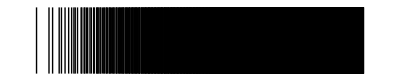

```mathematica
Graphics[Line[{{10#,0},{10#,12}}&/@Log[Last[FixedPointList[iter[#]&,{1}]]]]]
```

```mathematica
li1=Union[Sort[Flatten[Union[NestWhileList[2#&,#1,2#<350&],NestWhileList[3/2#&,#1,2#<350&],NestWhileList[4/3#&,#1,2#<350&],NestWhileList[5/4#&,#1,2#<350&]]&/@{1}]]];
```

```mathematica
Length[li1]
```

64

```mathematica
li2=Union[Sort[Flatten[Union[NestWhileList[2#&,#1,2#<350&],NestWhileList[3/2#&,#1,2#<350&],NestWhileList[4/3#&,#1,2#<350&],NestWhileList[5/4#&,#1,2#<350&]]&/@li1]]];
```

```mathematica
Length[li2]
```

643

```mathematica
li3=Union[Sort[Flatten[Union[NestWhileList[2#&,#1,2#<350&],NestWhileList[3/2#&,#1,2#<350&],NestWhileList[4/3#&,#1,2#<350&],NestWhileList[5/4#&,#1,2#<350&]]&/@li2]]];
```

```mathematica
Length[li3]
```

1554

```mathematica
li4=Union[Sort[Flatten[Union[NestWhileList[2#&,#1,2#<350&],NestWhileList[3/2#&,#1,2#<350&],NestWhileList[4/3#&,#1,2#<350&],NestWhileList[5/4#&,#1,2#<350&]]&/@li3]]];
```

```mathematica
Length[li4]
```

1554

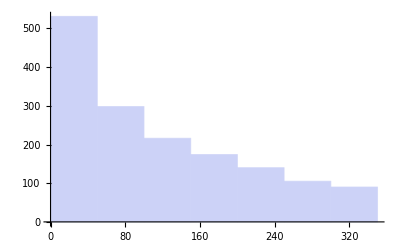

```mathematica
Histogram[li3,7]
```

```mathematica
N[li3[[1410]]]/N[li3[[1403]]]
```

1.00777

```mathematica
N[li3[[1403;;1410]]]
```

{269.48,269.695,270.,270.305,270.961,271.051,271.267,271.574}

```mathematica
N[li3[[1403]]]
```

269.48